Graficas velocidad de propagacion

Puntos sin errores (para hacer el fit lineal se usa la lista sin errores).

```mathematica
xy={{0,119.8},{2,162.1},{4,203.8},{6,245.3},{10,326.2},{13.2,387.4},{16.4,448.6},{19.6,509.7},{12.8,370.9},{38.4,880.6}};
```

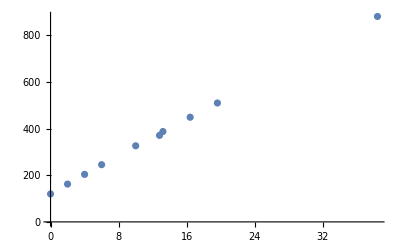

```mathematica
ListPlot[xy]
```

```mathematica
LinearModelFit[xy,x,x]
```

FittedModel[123.962+19.7286 x]

```mathematica
xyb={ {-6.2,119.5},{-2.2,201.1},{3,301.3},{9.2,421.7},{14.2,523.9},{15.8,545.2} ,{16.8,566.4},{17.8,587.7} ,{-5.2,142.2},{-4.2,163.5},{-3.2,184.8} ,{-2,206.1},{-1.2,222.4},{-0.2,243.7},{1.2,265},{2.4,286.3},{4.2,322.6},{5.4,343.9},{6.6,365.2},{7.6,386.9}}
```

{{-6.2,119.5},{-2.2,201.1},{3,301.3},{9.2,421.7},{14.2,523.9},{15.8,545.2},{16.8,566.4},{17.8,587.7},{-5.2,142.2},{-4.2,163.5},{-3.2,184.8},{-2,206.1},{-1.2,222.4},{-0.2,243.7},{1.2,265},{2.4,286.3},{4.2,322.6},{5.4,343.9},{6.6,365.2},{7.6,386.9}}

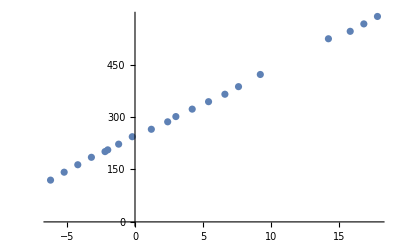

```mathematica
ListPlot[xyb]
```

```mathematica
LinearModelFit[xyb,x,x]
```

FittedModel[243.013+19.2876 x]

Modelos con barras de error (para graficar).

```mathematica
Needs["ErrorBarPlots`"];
```

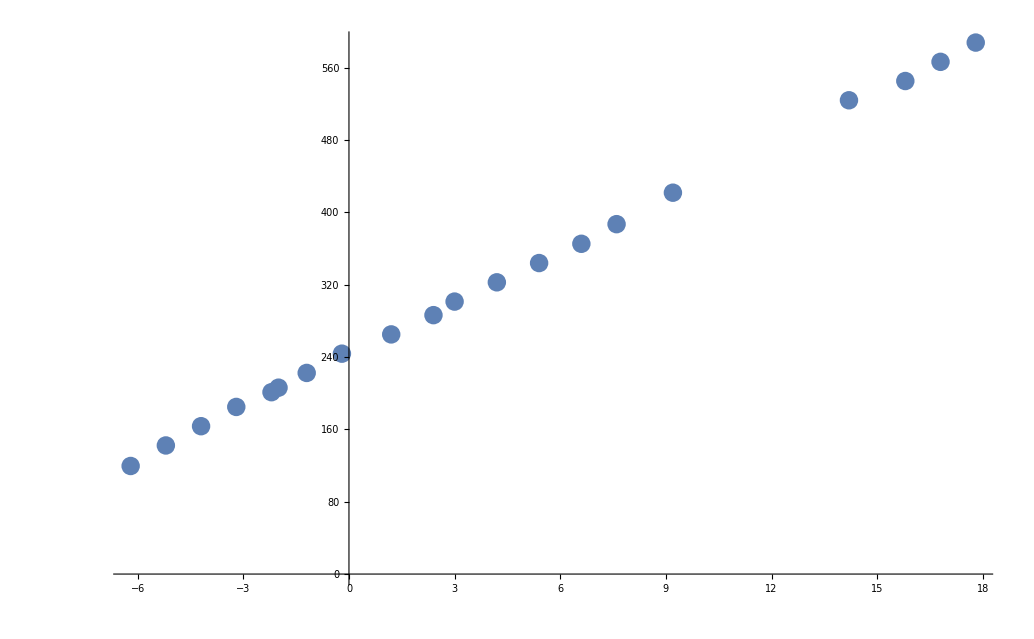

```mathematica
xybe=ErrorListPlot[{ {{-6.2,119.5},ErrorBar[0.2,0.5]},{{-2.2,201.1},ErrorBar[0.2,0.5]},{{3,301.3},ErrorBar[0.2,1]},{{9.2,421.7},ErrorBar[0.2,1.5]},{{14.2,523.9},ErrorBar[0.2,2.0]},{{15.8,545.2} ,ErrorBar[0.2,2.5]},{{16.8,566.4},ErrorBar[0.2,3]},{{17.8,587.7} ,ErrorBar[0.2,3.5]},{{-5.2,142.2},ErrorBar[0.2,1]},{{-4.2,163.5},ErrorBar[0.2,1.5]},{{-3.2,184.8} ,ErrorBar[0.2,2]},{{-2,206.1},ErrorBar[0.2,2.5]},{{-1.2,222.4},ErrorBar[0.2,1]},{{-0.2,243.7},ErrorBar[0.2,1.5]},{{1.2,265},ErrorBar[0.2,2]},{{2.4,286.3},ErrorBar[0.2,2.5]},{{4.2,322.6},ErrorBar[0.2,3]},{{5.4,343.9},ErrorBar[0.2,3.5]},{{6.6,365.2},ErrorBar[0.2,2]},{{7.6,386.9},ErrorBar[0.2,2.5]}}]
```

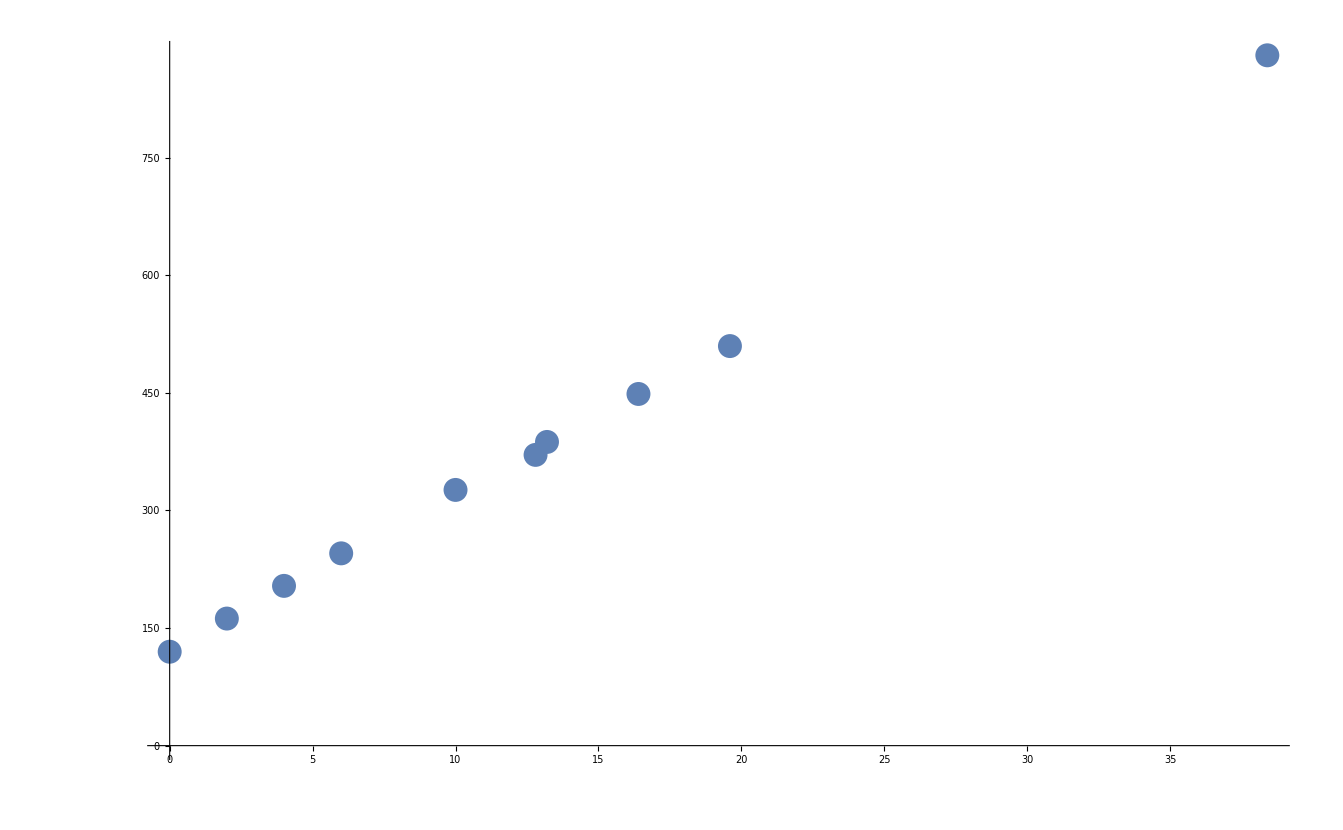

```mathematica
xye=ErrorListPlot[{{{0,119.8},ErrorBar[0.2,0.5]},{{2,162.1},ErrorBar[0.2,1]},{{4,203.8},ErrorBar[0.2,1.5]},{{6,245.3},ErrorBar[0.2,2]},{{10,326.2},ErrorBar[0.2,2.5]},{{13.2,387.4},ErrorBar[0.2,3]},{{16.4,448.6},ErrorBar[0.2,3.5]},{{19.6,509.7},ErrorBar[0.2,4]},{{12.8,370.9},ErrorBar[0.2,4.5]},{{38.4,880.6},ErrorBar[0.2,1]}}]  (*Para esta grafica la escala de tiempo es demasiado grande para apreciar el error, si puedes ajustar el tamaño de los puntos podrias ver las barras de error, estoy averiguando como hacer esto. *)
```

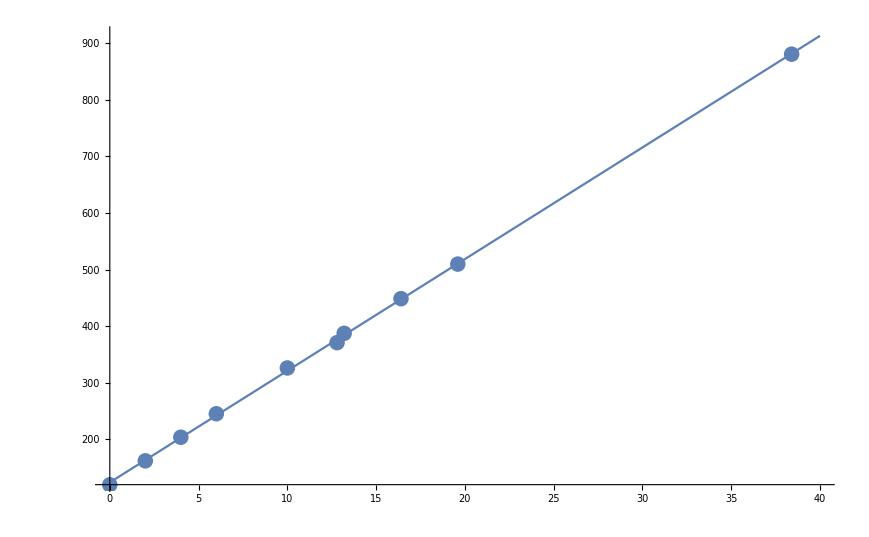

```mathematica
Show[Plot[123.96188482570051+19.728604180906817 x,{x,0,40}],xye]
```

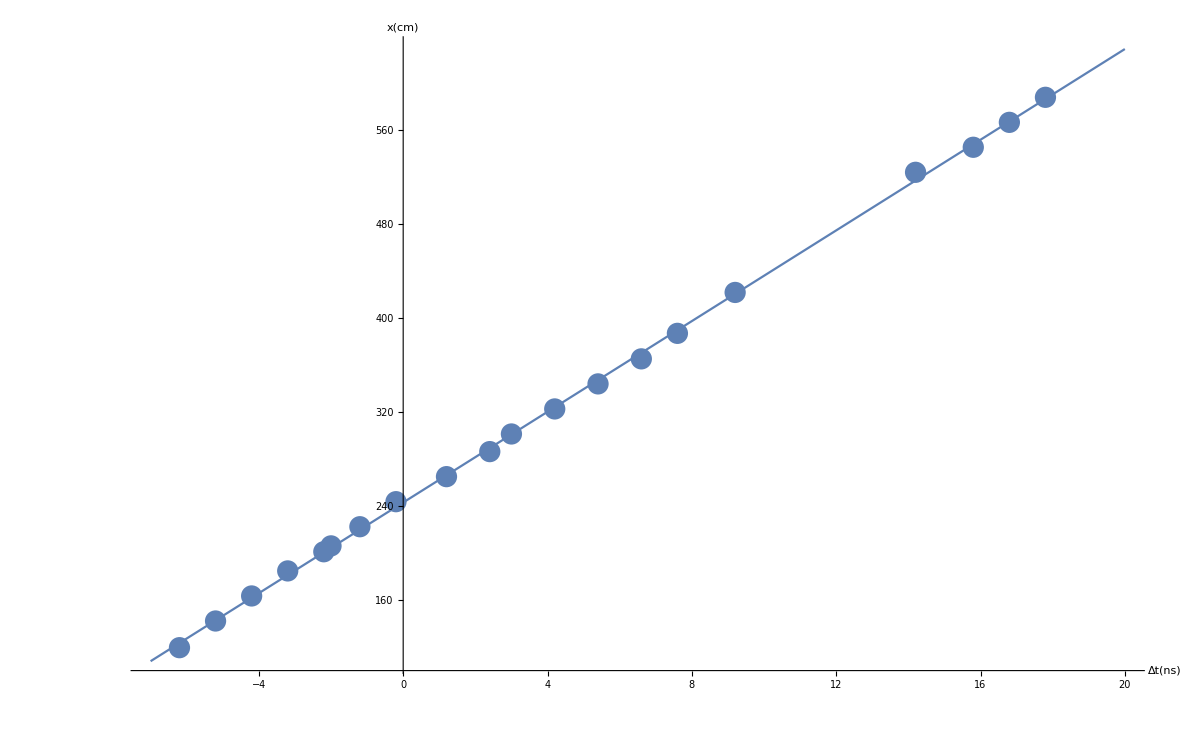

```mathematica
Show[Plot[243.01254363367806+19.28758304920349 x,{x,-7,20},AxesLabel->{"Δt(ns)", "x(cm)"}],xybe]
```